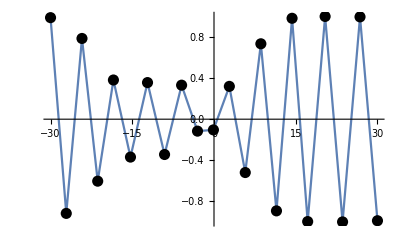

```mathematica
Plot[Sin[x],{x,-30,30},PlotPoints->6,MaxRecursion->2,Mesh->All,MeshStyle->PointSize[0.02]]
```

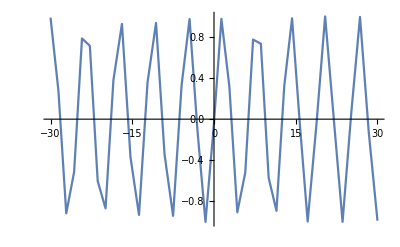

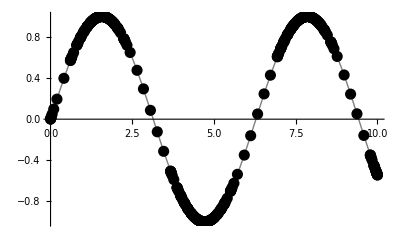

```mathematica
Plot[Sin[x],{x,0,10},Mesh->All,MeshStyle->PointSize[0.02],PlotStyle->{Thick,Gray}]
```

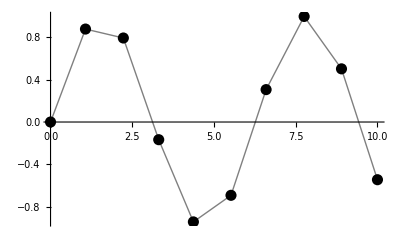

```mathematica
Plot[Sin[x],{x,0,10},Mesh->All,MeshStyle->PointSize[0.02],PlotStyle->{Thick,Gray},PlotPoints->10,MaxRecursion->0]
```

```mathematica
Reap[p=Plot[Sin[x],{x,0,10},PlotPoints->10,MaxRecursion->0,EvaluationMonitor:>Sow[x]];]
```

{Null,{{1.11111×10^-6,1.06867,2.22723,3.30902,4.36958,5.52004,6.59372,7.75729,8.89964,10.}}}

```mathematica
Manipulate[Plot[Sin[x],{x,0,Pi},Method->{Refine->},Mesh->All,MeshStyle->{Red,PointSize[Large]},PlotPoints->8],{n,0,90,2}]
```

```mathematica
Short[InputForm[p]]
```

p